```mathematica
maxocc=6;
nsites=4;
(*A Three well, linear lattice with NN hopping*)
graphDistance=GraphDistanceMatrix[Graph[{
UndirectedEdge[1,2],
UndirectedEdge[2,3],
UndirectedEdge[3,1]}]];
csb=Tuples[Range[maxocc+1]-1,nsites];
csb=SortBy[csb,Total];
Dimensions[csb]
(*kb=Tuples[Range[2]-1,3];
Outer[Join,csb,kb,1];*)
BasisSize=Dimensions[csb][[1]];
NumBlock=maxocc*nsites+1;
BlockSizes=Table[0,{i,NumBlock}];
k=0;
For[i=1,i<BasisSize+1,i++,
{k=If[k<(Total[csb[[i,All]]]+1),Total[csb[[i,All]]]+1,k],BlockSizes[[k]]++}];
```

{2401,4}

```mathematica
BlockCompare=Table[Sum[BlockSizes[[k]],{k,1,l}],{l,NumBlock}];

(*This gives the size of each block with certain total number of atoms*)
```

```mathematica
(*construct Subscript[σ, i,j] to show connectivity. The first step is to find which block a state with with index i is in, say i=BlockindexFinder. This can be done with comparing i with a list of number which is the total numbers of state before Block X. Then we can find the state with index j will connect with it. j has to be in the same Block for the atom number conservation, which leads to BlockCompare[[X-1]]<j≤BlockCompare[[X]].An algarithm needs to be derived in order to decide which elements are connected by moving *)
```

```mathematica
BlockCompare
```

{1,5,15,35,70,126,210,326,475,655,861,1085,1316,1540,1746,1926,2075,2191,2275,2331,2366,2386,2396,2400,2401}

```mathematica
(*i=5;
m=1;
While[i>BlockCompare[[m]],m++];
BlockindexFinder=m;*)
```

```mathematica
σ=List[];
hopHamiltonian=List[];
For[i=2,i<BasisSize+1,i++,
{m=1;
While[i>BlockCompare[[m]],m++];
BlockindexFinder=m;
For[j=BlockCompare[[BlockindexFinder-1]]+1,j<BlockCompare[[BlockindexFinder]]+1,j++,{BasisDifference=Table[csb[[j,n]]-csb[[i,n]],{n,nsites}],
diff=Ordering[BasisDifference,1]-Ordering[BasisDifference,-1],
p1=Ordering[BasisDifference,1][[1]],
p2=Ordering[BasisDifference,-1][[1]],
(*p1 and p2 record which position the excange happens*)
If[Sum[BasisDifference[[n]],{n,1,nsites}]==0&&
Norm[BasisDifference]==Sqrt[2]&&
(Abs[diff[[1]]]==1||Abs[diff[[1]]]==nsites-1),
(*graphDistance[[p1,p2]]==1,*)
σ=Append[σ,{i,j}];
hopHamiltonian=Append[hopHamiltonian,Sqrt[csb[[j,p1]]+1]*Sqrt[csb[[j,p2]]]],
0]
(*Select only nearest neighbor hopping, and add to the list of connected pairs. *)
}
]
}
]
σ=Append[σ,{BasisSize,BasisSize}];
sigmaSize=Dimensions[σ][[1]];
hopHamiltonian=Append[hopHamiltonian,0];
csselfinter=Table[Sum[csb[[i,n]](csb[[i,n]]-1),{n,1,nsites}],{i,BasisSize}];
cstotal=Table[Total[csb[[i,All]]],{i,BasisSize}];
(*For[k=1,k<sigmaSize+1,k++,Print[{σ[[k,1]],σ[[k,2]]},csb[[σ[[k,1]],All]],csb[[σ[[k,2]],All]],hopHamiltonian[[k]]]]*)
```

```mathematica
(*σ matrix shows which two elements inside the basis are connected by the hopping term*)
```

```mathematica
(*interaction term*)
Ucs=1.;
μcs=1.5;
apparentJ4=List[];
entropyJ4=List[];
hoppingJ=List[];
beforeappJ4=List[];
afterappJ4=List[];
(*Use a for loop to Plot entropy over J/U*)
For[J=10^-3.,J<10^6.,J=J+10^Floor[Log10[J]],
{
(*define the interaction strength and chemical potential, using hopping term J as unit, J=1*)
hopMat=SparseArray[σ->J*hopHamiltonian];
interactionMat=DiagonalMatrix[csselfinter*Ucs/2-cstotal*μcs];
HamiltonianMat=hopMat+interactionMat;

eigensystem=Eigensystem[N[HamiltonianMat]];
energy=eigensystem[[1]];
state=eigensystem[[2]];
pground=Ordering[energy,1][[1]];
groundvector=state[[pground]];
measuresite=1;
(*assuming measuring the first site*)

(*csbreshape=ArrayReshape[csb,{5,BasisSize}]//MatrixForm;
csbreshape[[1]]//MatrixForm
csbreshape//MatrixForm
joined = Join[state,csbreshape[[All,1]]]//MatrixForm;*)
(*
limit=250;
basisindex=Ordering[Abs[groundvector],-limit];
(*For[i=1,i<limit+1,i++,Print[csb[[basisindex[[i]]]],groundvector[[basisindex[[i]]]]]]*)
(*This is for printing out the ground state with basis and corresponding amplitude*)
Prob=Table[0,{i,maxocc+1}];

For[i=1,i<BasisSize+1,i++,If[groundvector[[i]]≠0,Prob[[csb[[i,measuresite]]+1]]=Prob[[csb[[i,measuresite]]+1]]+(groundvector[[i]])^2,0]]
ListPlot[Prob]

(*mean=Sum[Prob[[i]]*(i-1),{i,maxocc}]
StandardDeviation[Prob]*)(*this part has not verified for superfluid phase yet*)
*)
(*
t=10;
evolMat=MatrixExp[-N[HamiltonianMat]*t]//MatrixForm;
tinitial=SparseArray[{1}->0,BasisSize,1];
initial=ArrayReshape[initial,{BasisSize,1}];
evolMat.initial;
*)
(*ρMat=Outer[Times,groundvector,groundvector];*)
(*create density matrix by taking outproduct of the initial vector*)
(*t=1;
For[i=1,i<BasisSize+1,i++,t=t*(ρMat[[i]]==ρMat[[All,i]])]
t*)(*to verify ρMat is sysmetric*)
(*possiblebasis=List[];
possiblebasisindex=List[];
For[i=1,i<BasisSize+1,i++,If[groundvector[[i]]≠0,possiblebasis=Append[possiblebasis,groundvector[[i]]];possiblebasisindex=Append[possiblebasisindex,i],0]]
possiblebasisSize=Dimensions[possiblebasis][[1]]
initialdensityMatrix=Outer[Times,possiblebasis,possiblebasis];
Tr[initialdensityMatrix]
MatrixPower[initialdensityMatrix,2]==initialdensityMatrix

(*for a pure state, trace[ρ]=1,ρ^2=ρ, which verifies that this is a density Matrix*)

subpotentialindex0=List[];
subpotentialindex1=List[];
subpotentialindex2=List[];
subpotentialindex3=List[];
subpotentialindex4=List[];
subpotentialindex5=List[];
subpotentialindex6=List[];
For[i=1,i<possiblebasisSize+1,i++,
{
If[csb[[possiblebasisindex[[i]],measuresite]]==0,subpotentialindex0=Append[subpotentialindex0,possiblebasisindex[[i]]]],
If[csb[[possiblebasisindex[[i]],measuresite]]==1,subpotentialindex1=Append[subpotentialindex1,possiblebasisindex[[i]]]],
If[csb[[possiblebasisindex[[i]],measuresite]]==2,subpotentialindex2=Append[subpotentialindex2,possiblebasisindex[[i]]]],
If[csb[[possiblebasisindex[[i]],measuresite]]==3,subpotentialindex3=Append[subpotentialindex3,possiblebasisindex[[i]]]],
If[csb[[possiblebasisindex[[i]],measuresite]]==4,subpotentialindex4=Append[subpotentialindex4,possiblebasisindex[[i]]]],
If[csb[[possiblebasisindex[[i]],measuresite]]==5,subpotentialindex5=Append[subpotentialindex5,possiblebasisindex[[i]]]],
If[csb[[possiblebasisindex[[i]],measuresite]]==6,subpotentialindex6=Append[subpotentialindex6,possiblebasisindex[[i]]]]
}
]
Dimensions[subpotentialindex0]
Dimensions[subpotentialindex1]
Dimensions[subpotentialindex2]
Dimensions[subpotentialindex3]
Dimensions[subpotentialindex4]
Dimensions[subpotentialindex5]
Dimensions[subpotentialindex6]*)

(*initialindex=Reverse[Ordering[Abs[groundvector]]];
(*in order to obtain the position of the nonzero components from the ground/initial state vector, ordering the absolute value (positions of zeros will be in front)and then reverse the order list. After that, using a "while" to only save the nonzero*)
nonzeroinitialindex=List[];
n=1;
t=initialindex[[1]];
groundvector[[t]]
While[Abs[groundvector[[t]]]>0,nonzeroinitialindex=Append[nonzeroinitialindex,t];n++;t=initialindex[[n]]]
nonzerodensitysize=Dimensions[nonzeroinitialindex][[1]]
ρindex=List[];
ρblock=List[];
For[i=1,i<nonzerodensitysize+1,i++,
{
For[j=1,j<nonzerodensitysize+1,j++,
{ρindex=Append[ρindex,{nonzeroinitialindex[[i]],nonzeroinitialindex[[j]]}];
ρblock=Append[ρblock,groundvector[[nonzeroinitialindex[[i]]]]*groundvector[[nonzeroinitialindex[[j]]]]]
}]
}
]
ρindex=Append[ρindex,{BasisSize,BasisSize}];
ρblock=Append[ρblock,groundvector[[BasisSize]]*groundvector[[BasisSize]]];
(*Add the lower right corner of the density matrix to ensure the right size*)
densityMat=SparseArray[ρindex-> ρblock];
(*Creating the density matrix by using sparse array takes much longer than directly taking the outproduct by using the initial state vector.*)*)

(*verify this method of sparse matrix*)
(*t=1;
For[i=1,i<BasisSize+1,i++,t=t*(densityMat[[i]]==densityMat[[All,i]])]
t

True^2401
densityMat==ρMat
True*)
(*creating reduced density matrix--measuring only subregion, e.g. only first site. Projectve measurement collapse the Hilbert space. Entanglement Entropy is ΣρLogρ*)

subbasisindex0=List[];
subbasisindex1=List[];
subbasisindex2=List[];
subbasisindex3=List[];
subbasisindex4=List[];
subbasisindex5=List[];
subbasisindex6=List[];
(*projectvector0=Table[0,{i,BasisSize}];
projectvector1=Table[0,{i,BasisSize}];
projectvector2=Table[0,{i,BasisSize}];
projectvector3=Table[0,{i,BasisSize}];
projectvector4=Table[0,{i,BasisSize}];
projectvector5=Table[0,{i,BasisSize}];
projectvector6=Table[0,{i,BasisSize}];*)
(*revise if using different maximum occupancy*)
For[i=1,i<BasisSize+1,i++,
{
If[csb[[i,measuresite]]==0,subbasisindex0=Append[subbasisindex0,i](*;projectvector0[[i]]=1*),0],
If[csb[[i,measuresite]]==1,subbasisindex1=Append[subbasisindex1,i](*;projectvector0[[i]]=1*),0],
If[csb[[i,measuresite]]==2,subbasisindex2=Append[subbasisindex2,i](*;projectvector0[[i]]=1*),0],
If[csb[[i,measuresite]]==3,subbasisindex3=Append[subbasisindex3,i](*;projectvector0[[i]]=1*),0],
If[csb[[i,measuresite]]==4,subbasisindex4=Append[subbasisindex4,i](*;projectvector0[[i]]=1*),0],
If[csb[[i,measuresite]]==5,subbasisindex5=Append[subbasisindex5,i](*;projectvector0[[i]]=1*),0],
If[csb[[i,measuresite]]==6,subbasisindex6=Append[subbasisindex6,i](*;projectvector0[[i]]=1*),0]
}
];
(*generate a projection vector of the basis size and only the positions in the subspace is 1*)
(*probmeasure0=(groundvector^2).projectvector0
probmeasure1=(groundvector^2).projectvector1
probmeasure2=(groundvector^2).projectvector2
probmeasure3=(groundvector^2).projectvector3
probmeasure4=(groundvector^2).projectvector4
probmeasure5=(groundvector^2).projectvector5
probmeasure6=(groundvector^2).projectvector6*)

subbasissize=Dimensions[subbasisindex0][[1]];
reducedρMat0=DiagonalMatrix[Table[groundvector[[subbasisindex0[[i]]]]*groundvector[[subbasisindex0[[i]]]],{i,subbasissize}]];
reducedρMat1=DiagonalMatrix[Table[groundvector[[subbasisindex1[[i]]]]*groundvector[[subbasisindex1[[i]]]],{i,subbasissize}]];
reducedρMat2=DiagonalMatrix[Table[groundvector[[subbasisindex2[[i]]]]*groundvector[[subbasisindex2[[i]]]],{i,subbasissize}]];
reducedρMat3=DiagonalMatrix[Table[groundvector[[subbasisindex3[[i]]]]*groundvector[[subbasisindex3[[i]]]],{i,subbasissize}]];
reducedρMat4=DiagonalMatrix[Table[groundvector[[subbasisindex4[[i]]]]*groundvector[[subbasisindex4[[i]]]],{i,subbasissize}]];
reducedρMat5=DiagonalMatrix[Table[groundvector[[subbasisindex5[[i]]]]*groundvector[[subbasisindex5[[i]]]],{i,subbasissize}]];
reducedρMat6=DiagonalMatrix[Table[groundvector[[subbasisindex6[[i]]]]*groundvector[[subbasisindex6[[i]]]],{i,subbasissize}]];
Reducedρ=reducedρMat0+reducedρMat1+reducedρMat2+reducedρMat3+reducedρMat4+reducedρMat5+reducedρMat6;
reducedρevalues=Eigenvalues[Reducedρ];
Dreducedρ=Dimensions[reducedρevalues];
SE=-Re[Sum[If[reducedρevalues[[i]]==0,0,reducedρevalues[[i]]Log[reducedρevalues[[i]]]],{i,Dreducedρ[[1]]}]];
entropyJ4=Append[entropyJ4,{J,SE}];

P0=Tr[reducedρMat0];
P1=Tr[reducedρMat0];
P2=Tr[reducedρMat0];
P3=Tr[reducedρMat0];
P4=Tr[reducedρMat0];
P5=Tr[reducedρMat0];
P6=Tr[reducedρMat0];

(*apparent entropy of normalized subspace*)
AE0=-Sum[If[reducedρMat0[[i,i]]==0.,0,1/P0*reducedρMat0[[i,i]]Log[1/P0*reducedρMat0[[i,i]]]],{i,Dreducedρ[[1]]}];
AE1=-Sum[If[reducedρMat1[[i,i]]==0.,0,1/P1*reducedρMat0[[i,i]]Log[1/P1*reducedρMat1[[i,i]]]],{i,Dreducedρ[[1]]}];
AE2=-Sum[If[reducedρMat2[[i,i]]==0.,0,1/P2*reducedρMat0[[i,i]]Log[1/P2*reducedρMat2[[i,i]]]],{i,Dreducedρ[[1]]}];
AE3=-Sum[If[reducedρMat3[[i,i]]==0.,0,1/P3*reducedρMat0[[i,i]]Log[1/P3*reducedρMat3[[i,i]]]],{i,Dreducedρ[[1]]}];
AE4=-Sum[If[reducedρMat4[[i,i]]==0.,0,1/P4*reducedρMat0[[i,i]]Log[1/P4*reducedρMat4[[i,i]]]],{i,Dreducedρ[[1]]}];
AE5=-Sum[If[reducedρMat5[[i,i]]==0.,0,1/P5*reducedρMat0[[i,i]]Log[1/P5*reducedρMat5[[i,i]]]],{i,Dreducedρ[[1]]}];
AE6=-Sum[If[reducedρMat6[[i,i]]==0.,0,1/P6*reducedρMat0[[i,i]]Log[1/P6*reducedρMat6[[i,i]]]],{i,Dreducedρ[[1]]}];

afterappJ4=Append[afterappJ4,{J,P0*AE0+P1*AE1+P2*AE2+P3*AE3+P4*AE4+P5*AE5+P6*AE6}];

(*apparentprob=Table[0,{i,maxocc+1}];
For[i=1,i<BasisSize+1,i++,
{If[csb[[i,2]]==0,apparentprob[[1]]=apparentprob[[1]]+groundvector[[i]]^2],
If[csb[[i,2]]==1,apparentprob[[2]]=apparentprob[[2]]+groundvector[[i]]^2],
If[csb[[i,2]]==2,apparentprob[[3]]=apparentprob[[3]]+groundvector[[i]]^2],
If[csb[[i,2]]==3,apparentprob[[4]]=apparentprob[[4]]+groundvector[[i]]^2],
If[csb[[i,2]]==4,apparentprob[[5]]=apparentprob[[5]]+groundvector[[i]]^2],
If[csb[[i,2]]==5,apparentprob[[6]]=apparentprob[[6]]+groundvector[[i]]^2],
If[csb[[i,2]]==6,apparentprob[[7]]=apparentprob[[7]]+groundvector[[i]]^2]
}
];
(*Print[apparentprob],*)
apparentent=Sum[If[apparentprob[[i]]==0.,0.,-apparentprob[[i]]Log[apparentprob[[i]]]],{i,7}];
apparentJ4=Append[apparentJ4,{J,apparentent}];*)



}
]
```

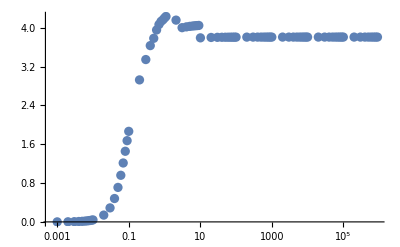

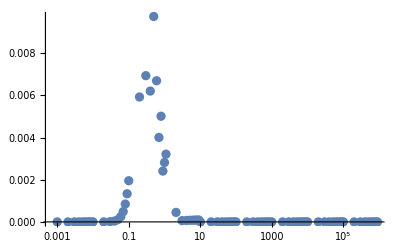

{{0.001,0.000625211},{0.002,0.00223539},{0.003,0.00468168},{0.004,0.00788654},{0.005,0.0117974},{0.006,0.016375},{0.007,0.0215888},{0.008,0.0274141},{0.009,0.0338307},{0.01,0.0408216},{0.02,0.140008},{0.03,0.288447},{0.04,0.481348},{0.05,0.709948},{0.06,0.959682},{0.07,1.21288},{0.08,1.4537},{0.09,1.6718},{0.1,1.86293},{0.2,2.9184},{0.3,3.33668},{0.4,3.62438},{0.5,3.77127},{0.6,3.94567},{0.7,4.0611},{0.8,4.12392},{0.9,4.15861},{1.,4.19615},{1.1,4.22772},{2.1,4.15497},{3.1,3.99995},{4.1,4.01664},{5.1,4.02694},{6.1,4.03393},{7.1,4.03898},{8.1,4.04281},{9.1,4.04581},{10.1,3.79059},{20.1,3.79835},{30.1,3.80098},{40.1,3.80229},{50.1,3.80309},{60.1,3.80362},{70.1,3.80399},{80.1,3.80428},{90.1,3.8045},{100.1,3.80468},{200.1,3.80547},{300.1,3.80574},{400.1,3.80587},{500.1,3.80595},{600.1,3.80601},{700.1,3.80604},{800.1,3.80607},{900.1,3.8061},{1000.1,3.80611},{2000.1,3.80619},{3000.1,3.80622},{4000.1,3.80623},{5000.1,3.80624},{6000.1,3.80625},{7000.1,3.80625},{8000.1,3.80625},{9000.1,3.80626},{10000.1,3.80626},{20000.1,3.80626},{30000.1,3.80627},{40000.1,3.80627},{50000.1,3.80627},{60000.1,3.80627},{70000.1,3.80627},{80000.1,3.80627},{90000.1,3.80627},{100000.,3.80627},{200000.,3.80627},{300000.,3.80627},{400000.,3.80627},{500000.,3.80627},{600000.,3.80627},{700000.,3.80627},{800000.,3.80627},{900000.,3.80627}}

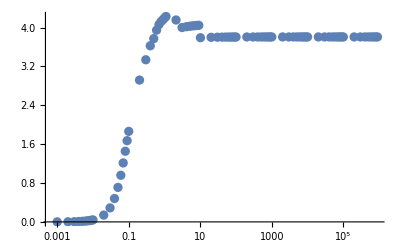

```mathematica
ListLogLinearPlot[entropyJ4,PlotRange->All]
ListLogLinearPlot[afterappJ4,PlotRange->All]
(*Jindex=Table[entropyJ4[[i,1]],{i,Dimensions[entropyJ4][[1]]}];
Sub=Table[afterappJ4[[i,2]]-entropyJ4[[i,2]],{i,Dimensions[entropyJ4][[1]]}];*)
Sub1=Table[{entropyJ4[[i,1]],-afterappJ4[[i,2]]+entropyJ4[[i,2]]},{i,Dimensions[entropyJ4][[1]]}]
ListLogLinearPlot[Sub1,PlotRange->All]
```

```mathematica
(*For[i=1,i<Dimensions[entropyJ4][[1]]+1,i++,Print[entropyJ4[[i,2]]/afterappJ4[[i,2]]]]*)
```